```mathematica
LaneEmden = ξ*θ''[ξ]+2θ'[ξ]+ξ*θ[ξ]^n== 0; (*1/ξ^2∂_ξ (ξ^2∂_ξ θ[ξ])+θ[ξ]^n== 0*)
```

```mathematica
SeriesSolution = AsymptoticDSolveValue[{LaneEmden, θ[0] == 1}, θ[ξ], {ξ,0,8}]
```

1-ξ^2/6+(n ξ^4)/120+((5 n-8 n^2) ξ^6)/15120+(n (70-183 n+122 n^2) ξ^8)/3265920

```mathematica
AnalyticalSolution = DSolve[{LaneEmden /. n-> 1,θ[0]==1, θ'[0]== 0}, θ[ξ],ξ]
SimplifiedSolution = FullSimplify[θ[ξ] /. AnalyticalSolution ]
```

{{θ[ξ]→-(ⅈ ⅇ^(-ⅈ ξ) (-1+ⅇ^(2 ⅈ ξ)))/(2 ξ)}}

{Sin[ξ]/ξ}

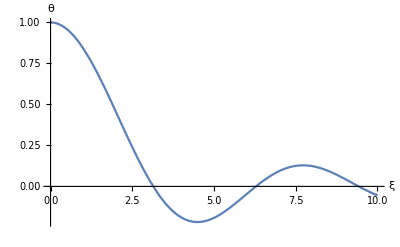

```mathematica
Plot[SimplifiedSolution,{ξ,0,10},PlotRange->All, AxesLabel -> {ξ,θ}]
```